```mathematica
(*Mathematica notebook to generate GCL connectivity
Guy Billings 2013*)
```

```mathematica
(*SetDirectory so that file works from within DropBox using the Code version in DropBox*)
```

```mathematica
SetDirectory[NotebookDirectory[]]
SetDirectory["../../Code/GCL-Mathematica-toolbox/"]
```

/home/eugenio/Dropbox/GCLpaper/Billings_etal_Silver_paper_2013/Neuron_Submission/Neuron_rev

/home/eugenio/Dropbox/GCLpaper/Billings_etal_Silver_paper_2013/Code/GCL-Mathematica-toolbox

```mathematica
(*Import library functions related to the TissueModel*)
Import["TissueModel.m"]
```

grcinvol::shdw: Symbol "grcinvol" appears in multiple contexts {"TissueModel`", "Global`"}; definitions in context "TissueModel`" may shadow or be shadowed by other definitions.

grcpos::shdw: Symbol "grcpos" appears in multiple contexts {"TissueModel`", "Global`"}; definitions in context "TissueModel`" may shadow or be shadowed by other definitions.

glopos::shdw: Symbol "glopos" appears in multiple contexts {"TissueModel`", "Global`"}; definitions in context "TissueModel`" may shadow or be shadowed by other definitions.

confineglom::shdw: Symbol "confineglom" appears in multiple contexts {"TissueModel`", "Global`"}; definitions in context "TissueModel`" may shadow or be shadowed by other definitions.

ALGconnections::shdw: Symbol "ALGconnections" appears in multiple contexts {"TissueModel`", "Global`"}; definitions in context "TissueModel`" may shadow or be shadowed by other definitions.

denlendist::shdw: Symbol "denlendist" appears in multiple contexts {"TissueModel`", "Global`"}; definitions in context "TissueModel`" may shadow or be shadowed by other definitions.

Amatrix::shdw: Symbol "Amatrix" appears in multiple contexts {"TissueModel`", "Global`"}; definitions in context "TissueModel`" may shadow or be shadowed by other definitions.

```mathematica
(*Diameter of tissue ball in microns*)
Diam=80;
```

```mathematica
(*SeedRandom[1*Round[Date[][[6]]]]*)
(*Number MFs populating the larger embedding volume. Should not need to change*)
nummf=2745; 
(*Number of connections for each GRC*)
d=4;
(*Dimensions of the embedding geometry: eg. side length if embedding geom is a cube*)
biglen=200;
(*Empirical distribution of glom per MF, taken from Sultan, does not have any material affect given the connectivity settings used - ask me about it if you want to know what that means - but it need to be here nevertheless*)
rdist={45,17,8,5};
(*glomerular x-spacing*)
glox=60;
(*glomerular y-spacing*)
gloy=20;
(*glomerular z-spacing*)
gloz=2;
(*embedding geometry. should not need to change*)
embedinggeom="cube";
(*geometry of the local network. shold not need to change*)
samplegeom="sphere";
(*target soft-constrained dnedrite length*)
dlen=15;
(*spatial scale of random exponentially distributed input correlations*)
corr=0;
```

```mathematica
?ALGconnections
```

ALGconnections[dlen_, mflist_, grclist_, d_, mossyrepeat_, force_] Algorithmic connections function : 
Ensures that the connections have an mf degree distribution that matches the random connection matrix and that all granule cells have exactly d connections. 
Aims to give an average connection length that is around a target value,  
but this is not gauranteed and the resultant distribution will depend on other parameters and sampling geometry. mossyrepeat = 0 : prevents TARGET degree distribution from reconnecting to identical mossy fibres through independent connections,mossyrepeat = 1 : Allows repeat sampling of mossy fibres.mossyrepeat = 2 : does not allow repeat sampling and also forces the mossy fibres to be connected with equal probability(i.e. does not randomly choose from glom list.)mossyrepeat also changes the degree distribution process so that the degree distribution is for granule cells that can only connect to a single mossy fibre once.force = 0 : Does not force a match between DDist and the degree distribution in the connection list.force = 1 : Force the degree distribution to be matched by the model connectivity, by rearranging connections.

```mathematica
(*compute positions of cells*)
glomraw=glopos[biglen,nummf,rdist,glox,gloy,gloz,embedinggeom];
glompos=DeleteCases[confineglom[glomraw,samplegeom,Diam],{}];
granpos=grcpos[biglen,Diam,grcinvol[Diam,samplegeom],samplegeom];


(*should not need to change the final 2 flags ('mossyrepeat' and 'force')*)
connsM=ALGconnections[dlen,glompos,granpos,d,2,1];
(*compute adjacency matrix*)
AmodelM=Amatrix[connsM[[1]]];
```

```mathematica
outputfile = NotebookDirectory[]<>"GCLconnectivity.graphml"
```

/home/eugenio/Dropbox/GCLpaper/Billings_etal_Silver_paper_2013/Neuron_Submission/Neuron_rev/GCLconnectivity.graphml

```mathematica
(*export to graphml*)
Export[outputfile,AmodelM[[2]]];
```

```mathematica
(*output glom. and GC position information*)
outputfile = NotebookDirectory[]<>"GLOMpositions.csv";
Export[outputfile,glompos]
outputfile = NotebookDirectory[]<>"GCpositions.csv";
Export[outputfile,granpos]
```

/home/eugenio/Dropbox/GCLpaper/Billings_etal_Silver_paper_2013/Neuron_Submission/Neuron_rev/GLOMpositions.csv

/home/eugenio/Dropbox/GCLpaper/Billings_etal_Silver_paper_2013/Neuron_Submission/Neuron_rev/GCpositions.csv

```mathematica
(*Visual check of the connectivity:*)
```

```mathematica
(*glom. degree distribution*)
```

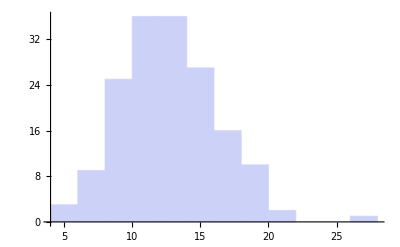

```mathematica
Histogram[Total[AmodelM[[1]]]]
```

```mathematica
?denlendist
```

denlendist[conns_, glompos_, granpos_] Distribution of granule cell dendrite length.

```mathematica
dlendist=denlendist[connsM[[1]],glompos,granpos];
```

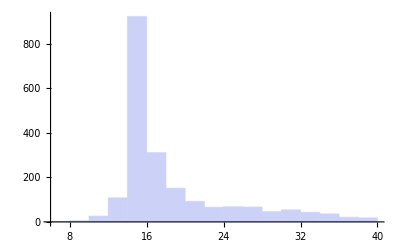

```mathematica
Histogram[Flatten[dlendist]]
```

```mathematica
GRAglom=Graphics3D[{Blue,Point[Flatten[glompos,1]]}];
```

```mathematica
GRAgrc=Graphics3D[{Red,PointSize[Large],Point[granpos]}];
```

```mathematica
Show[GRAglom,GRAgrc]
```

-Graphics3D-

-Graphics3D-